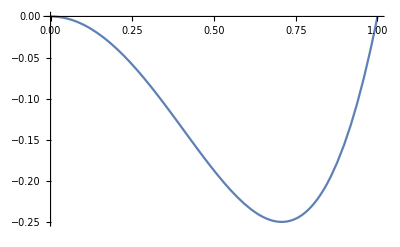

```mathematica
f[x_]:=-x^2+x^4
Plot[f[x],{x,0,1}]
```

```mathematica
g[z_]:=NIntegrate[1/Sqrt[-f[x]], {x,z,1}, WorkingPrecision->16, MaxRecursion->10]
```

```mathematica
Function[z,NIntegrate[1/(√(-f[x])),{x,z,1},WorkingPrecision->16,MaxRecursion->500]]
```

Function[z,NIntegrate[1/(√(-f[x])),{x,z,1},WorkingPrecision→16,MaxRecursion→500]]

```mathematica
g[10^-100]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in x near {x} = {1.56526445426632970093708904832406353606328358601940804102317241723×10^-57}. NIntegrate obtained 225.591413035365510847233065805748637530674116811784409358497991034 and 26.7440750410174563485253136947905305794979283721111593625754434024 for the integral and error estimates.

225.5914130353655

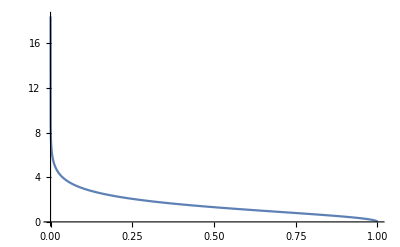

```mathematica
Plot[g[c],{c,1*^-15,1}, PlotRange->All]
```

```mathematica
AsymptoticIntegrate[1/Sqrt[-f[x]],{x,0,1},x->0]
```

AsymptoticIntegrate[1/(√(x^2-x^4)),{x,0,1},x→0]

```mathematica
AsymptoticIntegrate[f[x],{x,0,∞},{ω,∞,1}]
```

AsymptoticIntegrate[-x^2+x^4,{x,0,∞},{ω,∞,1}]

```mathematica
h[x_,k_]:=1/(2*Sqrt(x*(1-x)*(x-1+k^2)))
```

```mathematica
Series[h[x,k], {1-k,1,3}]
```

General::ivar: 1-k is not a valid variable.

Series[1/(2 Sqrt (1-x) x (-1+k^2+x)),{1-k,1,3}]

```mathematica
int[x_]:=2*Integrate[Sqrt[(Cos[k])^2+x^2*(Sin[k])^2],{k,0,π/2}, Assumptions->x∈Reals]
```

```mathematica
Series[int[x],{x,0,3}]
```

Floor[(π-2 Arg[x])/(2 π)] (-ⅈ π x^2+O[x]^3)+(2+2 (-1/4+Log[2]-Log[x]/2) x^2+O[x]^3)

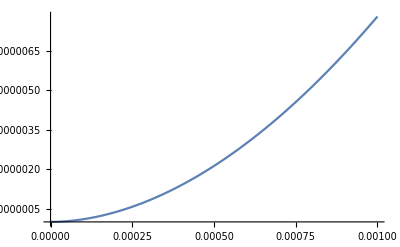

```mathematica
Plot[int[s],{s,0,0.001}]
```

```mathematica
hj[x_]:=D[int[z],z].z->x
```

```mathematica
hj[0.1]//N
```

(-(2. z (EllipticE[1.-1. z^2]-1. EllipticK[1.-1. z^2]))/(1.-1. z^2)).z→0.1

```mathematica
N[%]
```

(-(2. z (EllipticE[1.-1. z^2]-1. EllipticK[1.-1. z^2]))/(1.-1. z^2)).z→0.1

```mathematica
FunctionExpand[Factorial2[n],Assumptions->n∈Integers]
```

2^(n/2+1/4 (1-Cos[n π])) π^(1/4 (-1+Cos[n π])) Gamma[1+n/2]

```mathematica
l[y_]:=1/(2*(Sqrt[y*(1-y)*(y-1+k^2)]))
```

```mathematica
l0[y_,eps_]:=1/(2*(Sqrt[y*(1-y)*(y-1+(1-eps)^2)]))
```

```mathematica
Series[l0[x,eps],{eps,0,3}]
```

1/(2 √(-(-1+x) x^2))+eps/(2 x √(-(-1+x) x^2))+((3-x) eps^2)/(4 x^2 √(-(-1+x) x^2))+((5-3 x) eps^3)/(4 x^3 √(-(-1+x) x^2))+O[eps]^4

```mathematica
TeXForm[x/Sqrt[5]]
```

\frac{x}{\sqrt{5}}